```mathematica
o[x_,y_]:=x+y
```

```mathematica
o[a1+1/x,b1+1/y]//Together
```

(x+y+a1 x y+b1 x y)/(x y)

```mathematica
o[a1+1/(a2+1/x),b1+1/y]//Together
```

(1+a2 x+a1 y+b1 y+x y+a1 a2 x y+a2 b1 x y)/((1+a2 x) y)

```mathematica
Factor[x y+a1 a2 x y+a2 b1 x y]
```

(1+a1 a2+a2 b1) x y

```mathematica
Factor[a1 x y+b1 x y]
```

(a1+b1) x y

```mathematica
Simplify[(1+a1 a2+a2 b1)/(1+a2)]
```

(1+a1 a2+a2 b1)/(1+a2)

```mathematica
o[a1+1/(1+a2,b1+1/y]
```

```mathematica
Together[o[a1+1/(a2+1/x), b1+1/y]/.{a1->1,a2->2,b1->10}]
```

(1+2 x+11 y+23 x y)/((1+2 x) y)

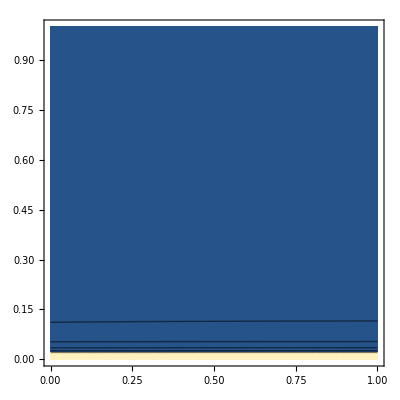

Indeterminate

```mathematica
ContourPlot[(1+2 x+11 y+23 x y)/((1+2 x) y),{x,0,1},{y,0,1},PlotRange->All]
```

```mathematica
Together[o[a1+1/x,b1+1/(b2+1/y)]]
```

(1+a1 x+b1 x+b2 y+x y+a1 b2 x y+b1 b2 x y)/(x (1+b2 y))

```mathematica
o[a1+1/x,b1+1/(b2+1/y)]
```

a1+b1+1/x+1/(b2+1/y)

```mathematica
o[a1+1/x,b1+1/y]
```

a1+b1+1/x+1/y

```mathematica
Together[o[a1+1/x,b1+1/y]]
```

(x+y+a1 x y+b1 x y)/(x y)

```mathematica
Numerator[Together[o[a1+1/(a2+1/x),b1+1/y]]]
```

1+a2 x+a1 y+b1 y+x y+a1 a2 x y+a2 b1 x y

```mathematica
Coefficient[Numerator[Together[o[a1+1/(a2+1/x),b1+1/y]]],x*y]
```

1+a1 a2+a2 b1

```mathematica
takeApart[ff_]:=
Module[{numerator, denominator,a,b,c,d,e,f,g,h},
numerator=Numerator[Together[ff]];
denominator=Denominator[Together[ff]];
a=Coefficient[numerator,x*y];
b=Coefficient[numerator,x]/.{y->0};
c=Coefficient[numerator,y]/.{x->0};
d=numerator/.{x->0,y->0};
e=Coefficient[denominator,x*y];
f=Coefficient[denominator,x]/.{y->0};
g=Coefficient[denominator,y]/.{x->0};
h=denominator/.{x->0,y->0};
Return[{a,b,c,d,e,f,g,h}]]
```

```mathematica
takeApart[o[a1+1/x,b1+1/y]]
```

{a1+b1,1,1,0,1,0,0,0}

```mathematica
takeApart[o[a1+1/(a2+1/x),b1+1/y]]
```

{1+a1 a2+a2 b1,a2,a1+b1,1,a2,0,1,0}

```mathematica
form1[ff_]:=
Module[{a,b,c,d,e,f,g,h},
{a,b,c,d,e,f,g,h}=takeApart[ff];
Return[
{Grid[{{b,d},{f,h}}],
Grid[{{a,c},{e,g}}]
}
]
]
```

```mathematica
form1[o[a1+1/x,b1+1/y]]
```

{1 | 0
0 | 0,a1+b1 | 1
1 | 0}

```mathematica
form1[o[a1+1/(a2+1/x),b1+1/y]]
```

{a2 | 1
0 | 0,1+a1 a2+a2 b1 | a1+b1
a2 | 1}

```mathematica
form1[o[a1+1/(a2+1/(a3+1/x)),b1+1/y]]
```

{1+a2 a3 | a2
0 | 0,a1+a3+a1 a2 a3+b1+a2 a3 b1 | 1+a1 a2+a2 b1
1+a2 a3 | a2}

```mathematica
form1[o[a1+1/x,b1+1/y]]
```

{1 | 0
0 | 0,a1+b1 | 1
1 | 0}

```mathematica
form1[o[a1+1/x,b1+1/(b2+1/y)]]
```

{a1+b1 | 1
1 | 0,1+a1 b2+b1 b2 | b2
b2 | 0}

```mathematica
(b*x+d) /(f*x + h)
```